```mathematica
hbarc = 0.197326938;
outputDir = "/Users/derek/github/freestream-milne/output";
```

```mathematica
initEnergyDensity = Import[outputDir<>"/initial_e.dat", "TSV"];
streamedEnergyDensity = Import[outputDir<>"/e.dat", "TSV"];
streamedPressure = Import[outputDir<>"/p.dat", "TSV"];
streamedBulkPressure = Import[outputDir<>"/bulk_PI.dat", "TSV"];
initEnergyDensityTable=Table[StringReplace[ToString[initEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@initEnergyDensity}];
streamedEnergyDensityTable=Table[StringReplace[ToString[streamedEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedEnergyDensity}];
streamedPressureTable=Table[StringReplace[ToString[streamedPressure[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedPressure}];
streamedBulkPressureTable=Table[StringReplace[ToString[streamedBulkPressure[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedBulkPressure}];
initEnergyDensityInterp = Interpolation[initEnergyDensityTable, InterpolationOrder->3];
streamedEnergyDensityInterp = Interpolation[streamedEnergyDensityTable, InterpolationOrder->3];
streamedPressureInterp = Interpolation[streamedPressureTable, InterpolationOrder->3];
streamedBulkPressureInterp = Interpolation[streamedBulkPressureTable, InterpolationOrder->3];
```

```mathematica
xlim = 10.0;
ylim = 10.0;
zlim = 2.5;
```

```mathematica
Initial Energy Density Transverse Profile
```

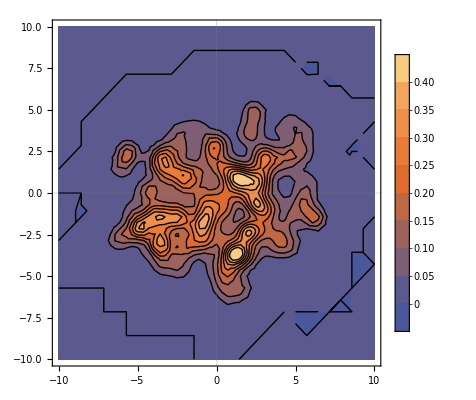

```mathematica
ContourPlot[initEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

```mathematica
Initial Energy Density Longitudinal Profile
```

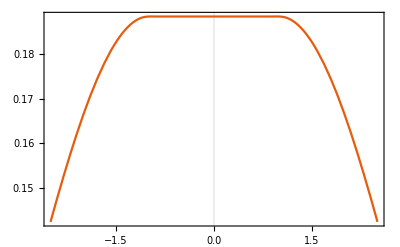

```mathematica
Plot[initEnergyDensityInterp[0,0,z], {z,-zlim,zlim},PlotLegends->Automatic, PlotTheme->"Scientific",PlotRange->All]
```

```mathematica
Energy Density Transverse Profile after 0.1 fm/c
```

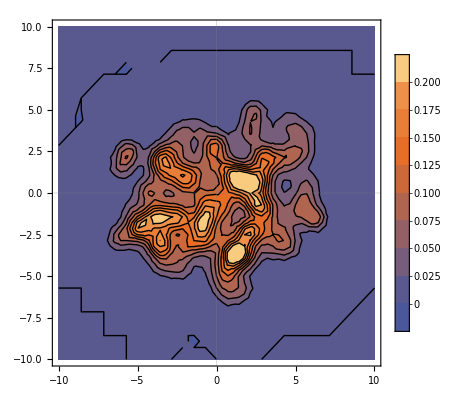

```mathematica
ContourPlot[streamedEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

```mathematica
Energy Density Longitudinal Profile after 0.1 fm/c
```

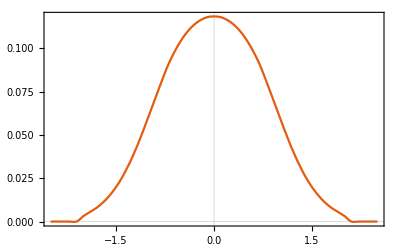

```mathematica
Plot[streamedEnergyDensityInterp[0,0,z], {z,-zlim,zlim},PlotLegends->Automatic, PlotTheme->"Scientific",PlotRange->All]
```

```mathematica
Bulk Pressure Profile after 0.1 fm/c
```

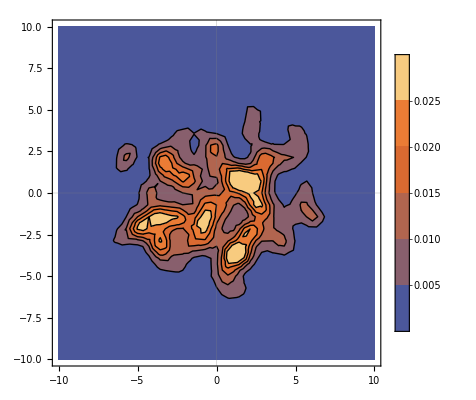

```mathematica
ContourPlot[streamedBulkPressureInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```

```mathematica
Pressure profile  after 0.1 fm/c
```

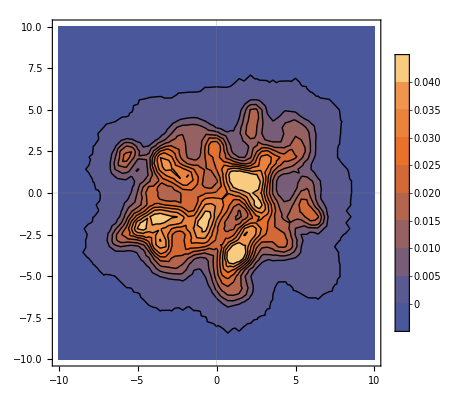

```mathematica
ContourPlot[streamedPressureInterp[x,y, 0],{x,-xlim, xlim},{y,-ylim,ylim}, PlotLegends->Automatic, PlotTheme->"Scientific", PlotRange->All]
```